```mathematica
SetDirectory[NotebookDirectory[]<>"..\\2009\\results"]
```

D:\Programs\icmm\speed\2009\results

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\2005\\results"]
```

D:\Работа\Programs\speed\2005\results

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\2012"]
```

D:\Programs\icmm\speed\2012

```mathematica
ReadData[name_]:=Block[{st=OpenRead[name],dump={1},meshs,test},Read[st,String];While[Last[dump]=!=EndOfFile,AppendTo[dump,Read[st,Number]];Skip[st,Character,24];AppendTo[dump,Read[st,Number]];Skip[st,Character,12];AppendTo[dump,Read[st,Number]];Skip[st,Character,12];AppendTo[dump,Read[st,Number]];Skip[st,Character,15];AppendTo[dump,Read[st,Number]];Skip[st,String];];Close[st];dump;dump=Partition[Select[Rest[dump],NumericQ],5];
meshs=Union[Last/@dump];
test=Map[Function[mesh,Sort[Select[dump,Last[#1]==mesh&]]],meshs];
Return[test];];
ShowRel[l_,iter_:False]:=Block[{Iter1=((#1⟦4⟧)/(#1⟦2⟧)&)[l⟦1⟧],Total1=l⟦1,4⟧,byIter,byTotal},
byIter=({#1⟦1⟧,Iter1/((#1⟦4⟧)/(#1⟦2⟧))}&)/@l;byTotal=({#1⟦1⟧,Total1/(#1⟦4⟧)}&)/@l;If[iter,ListPlot[byIter,Joined->True,PlotLabel->"Time per 1 iteration on mesh "<>ToString[Last[l⟦1⟧]]<>"^3",PlotRange->All,AxesOrigin->{1,0}],ListPlot[byTotal,Joined->True,PlotLabel->"Total time on mesh"<>ToString[Last[l⟦1⟧]]<>"^3",PlotRange->All,AxesOrigin->{1,0}]];
ListPlot[byIter,Joined->True,PlotLabel->"Acceleration on mesh  "<>ToString[Last[l⟦1⟧]]<>"^2",PlotRange->All,AxesOrigin->{1,0},PlotMarkers->●]];
```

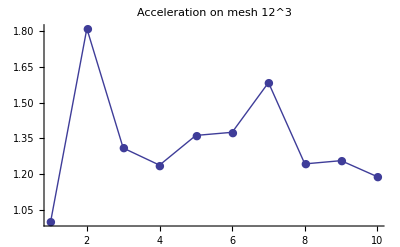
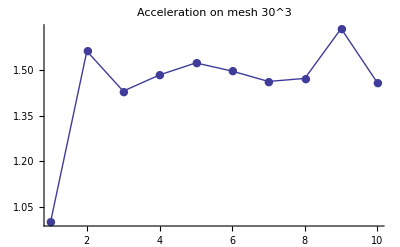
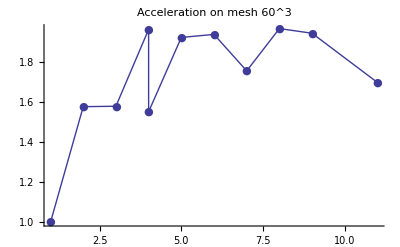
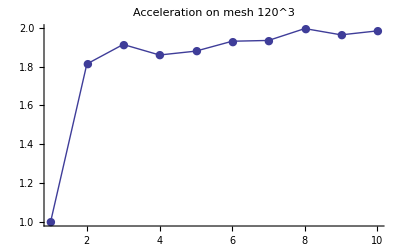

```mathematica
resAmazonka=ReadData["result(Amazonka).dat"];
grAmazonka=ShowRel[#,True]&/@resAmazonka
```

```mathematica
Manipulate[ListPlot[{#⟦1⟧,(#1⟦4⟧#⟦1⟧)/(#1⟦2⟧)}&/@{resTopsy,resIMM64,resPSTU}[[nl,nd]]],{nl,Range[3]},{nd,Range[4]}]
```

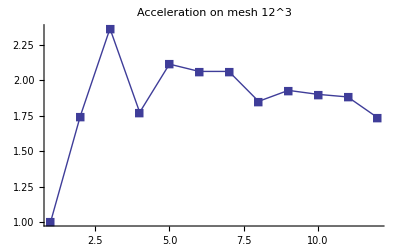
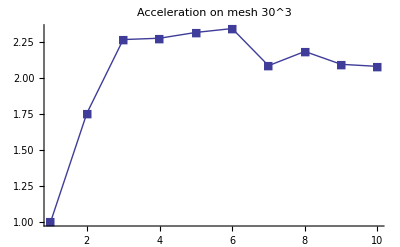
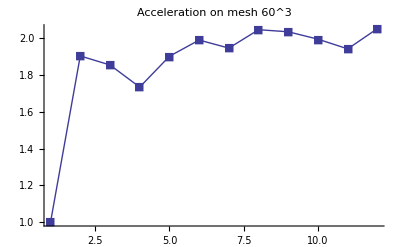
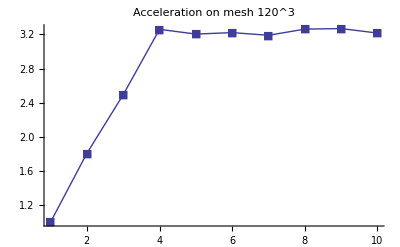

```mathematica
resTopsy=ReadData["result(Topsy).dat"];
grTopsy=ReplaceAll[ShowRel[#,False]&/@resTopsy,●->■]
```

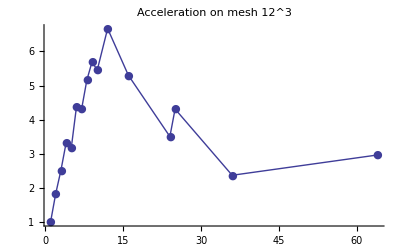
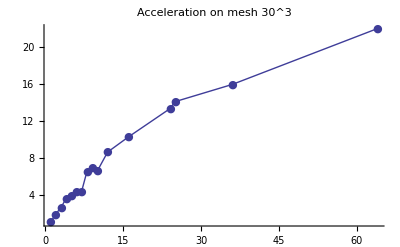
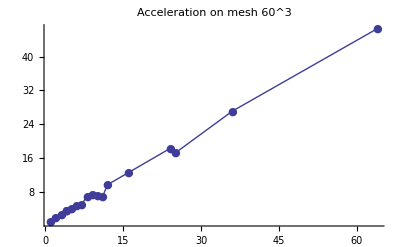
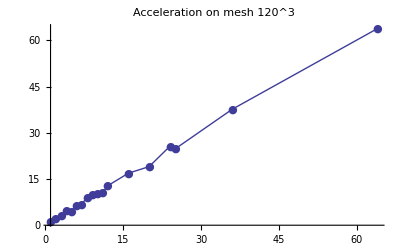

```mathematica
resIMM64=ReadData["result(IMM64).dat"];
grIMM64=ShowRel[#,True]&/@resIMM64
```

```mathematica
resIMM32=ReadData["result(IMM32).dat"];
ShowRel[#,True]&/@(*resIMM32*)
```

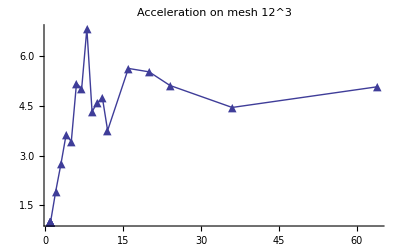
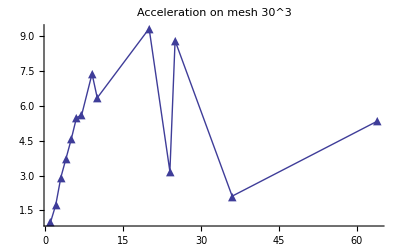
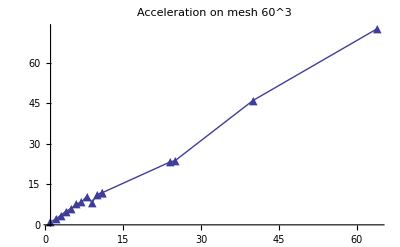
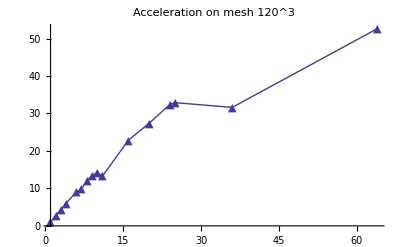

```mathematica
resPSTU=ReadData["result(PSTU).dat"];
grPSTU=ReplaceAll[ShowRel[#,True]&/@resPSTU,●->▲]
```

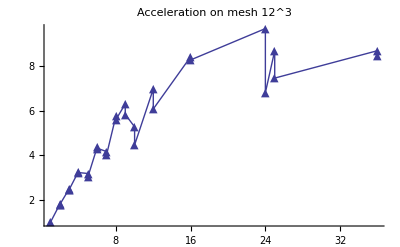
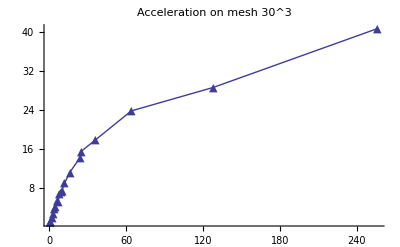
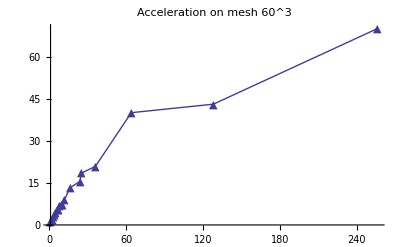
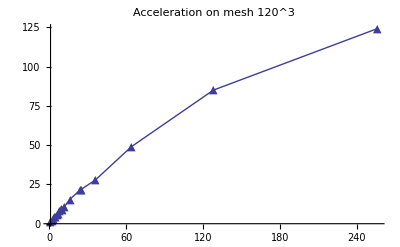
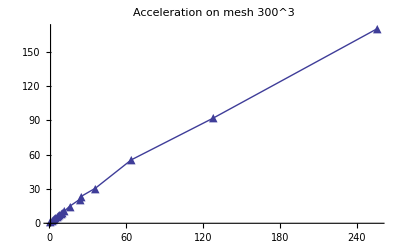

```mathematica
resLomonos=ReadData["result(Lomonosov).dat"];
grLomonos=ReplaceAll[ShowRel[#,True]&/@resLomonos,●->▲]
```

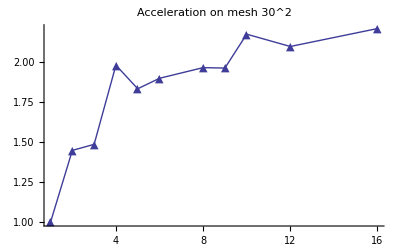
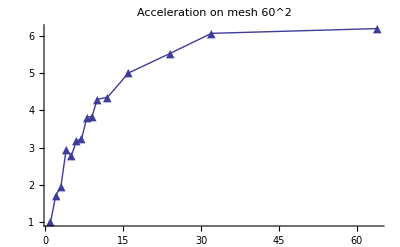
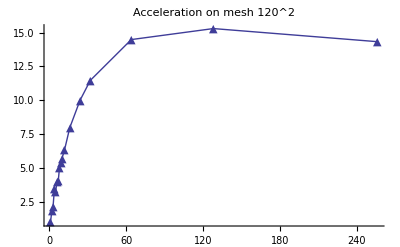
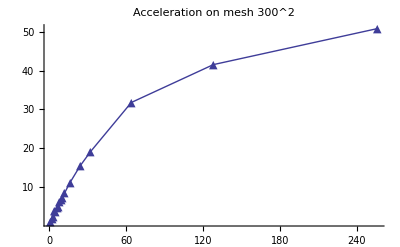

```mathematica
resLom2d=ReadData["result(Lomonosov).dat"];
grLom2d=ReplaceAll[ShowRel[#,True]&/@resLom2d,●->▲]
```

```mathematica
resLomonos//TableForm
```

1
5143
100.002
35.4359
12 | 2
5143
100.002
19.5884
12 | 2
5143
100.002
19.6403
12 | 2
5143
100.002
19.7495
12 | 3
5143
100.002
14.2053
12 | 3
5143
100.002
14.3551
12 | 3
5143
100.002
14.3795
12 | 4
5143
100.002
10.8204
12 | 4
5143
100.002
10.9934
12 | 5
5143
100.002
11.1369
12 | 5
5143
100.002
11.6901
12 | 6
5143
100.002
8.10799
12 | 6
5143
100.002
8.21109
12 | 7
5143
100.002
8.50893
12 | 7
5143
100.002
8.80013
12 | 8
5143
100.002
6.15434
12 | 8
5143
100.002
6.32851
12 | 9
5143
100.002
5.62277
12 | 9
5143
100.002
6.07574
12 | 10
5143
100.002
6.72156
12 | 10
5143
100.002
7.93896
12 | 12
5143
100.002
5.08053
12 | 12
5143
100.002
5.83234
12 | 16
5143
100.002
4.20879
12 | 16
5143
100.002
4.28166
12 | 24
5143
100.002
3.65988
12 | 24
5143
100.002
5.20683
12 | 25
5143
100.002
4.07896
12 | 25
5143
100.002
4.7496
12 | 36
5143
100.002
4.07771
12 | 36
5143
100.002
4.19192
12
1
4856
10.0011
1080.66
30 | 1
4856
10.0011
1080.99
30 | 1
4856
10.0011
1082.06
30 | 2
4856
10.0011
560.711
30 | 3
4856
10.0011
390.23
30 | 4
4856
10.0011
293.108
30 | 5
4856
10.0011
255.621
30 | 6
4856
10.0011
201.489
30 | 7
4856
10.0011
210.988
30 | 8
4856
10.0011
157.011
30 | 9
4856
10.0011
150.266
30 | 10
4856
10.0011
144.215
30 | 12
4856
10.0011
119.941
30 | 16
4856
10.0011
96.5801
30 | 24
4856
10.0011
76.0215
30 | 25
4856
10.0011
69.6209
30 | 36
4856
10.0011
60.5711
30 | 64
4856
10.0011
45.4292
30 | 128
4856
10.0011
37.7844
30 | 256
4856
10.0011
26.5812
30 |  |  |  |  |  |  |  |  |  |  | 
1
391
0.200076
717.805
60 | 2
391
0.200076
361.845
60 | 3
391
0.200076
257.624
60 | 4
391
0.200076
188.47
60 | 5
391
0.200076
166.359
60 | 6
391
0.200076
134.404
60 | 7
391
0.200076
128.107
60 | 8
391
0.200076
104.431
60 | 9
391
0.200076
100.573
60 | 10
391
0.200076
100.012
60 | 12
391
0.200076
79.5928
60 | 16
391
0.200076
54.4435
60 | 24
391
0.200076
46.1176
60 | 25
391
0.200076
38.8818
60 | 36
391
0.200076
34.3682
60 | 64
391
0.200076
17.9415
60 | 128
391
0.200076
16.68
60 | 256
391
0.200076
10.257
60 |  |  |  |  |  |  |  |  |  |  |  |  | 
1
80
0.0100096
1460.89
120 | 2
80
0.0100096
667.647
120 | 3
80
0.0100096
460.632
120 | 4
80
0.0100096
336.962
120 | 5
80
0.0100096
327.256
120 | 6
80
0.0100096
241.749
120 | 7
80
0.0100096
234.316
120 | 8
80
0.0100096
177.234
120 | 9
80
0.0100096
156.896
120 | 10
80
0.0100096
168.82
120 | 12
80
0.0100096
133.129
120 | 16
80
0.0100096
94.5837
120 | 24
80
0.0100096
68.1145
120 | 25
80
0.0100096
66.6567
120 | 36
80
0.0100096
52.4352
120 | 64
80
0.0100096
29.8241
120 | 128
80
0.0100096
17.1792
120 | 256
80
0.0100096
11.7601
120 |  |  |  |  |  |  |  |  |  |  |  |  | 
1
49
0.00100925
13363.8
300 | 2
49
0.00100925
6719.99
300 | 3
49
0.00100925
4829.84
300 | 4
49
0.00100925
3524.06
300 | 5
49
0.00100925
2797.09
300 | 6
49
0.00100925
2234.01
300 | 7
49
0.00100925
2059.13
300 | 8
49
0.00100925
1797.4
300 | 9
49
0.00100925
1529.38
300 | 10
49
0.00100925
1431.22
300 | 12
49
0.00100925
1230.43
300 | 16
49
0.00100925
895.967
300 | 24
49
0.00100925
635.019
300 | 25
49
0.00100925
566.65
300 | 36
49
0.00100925
435.626
300 | 64
49
0.00100925
240.933
300 | 128
49
0.00100925
145.185
300 | 256
49
0.00100925
78.4886
300 |  |  |  |  |  |  |  |  |  |  |  |  |

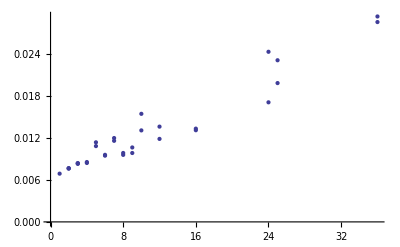

```mathematica
ListPlot[{#⟦1⟧,#⟦1⟧(#⟦4⟧)/(#⟦2⟧)}&/@resLomonos[[1]]]
```

```mathematica
Min[(#⟦1⟧)^0(#⟦4⟧)/((#⟦5⟧)^2#⟦2⟧)10^9&/@resLom2d[[4]]]
```

23.3672

```mathematica
Manipulate[With[{list=ToExpression["res"<>cluster][[First@First@Position[{12,30,60,120,300},mesh]]]},ListLogLogPlot[{#⟦1⟧,(((#⟦4⟧)/(#⟦2⟧)#⟦1⟧)/(list⟦1,4⟧/list⟦1,2⟧))^-1}&/@list,PlotRange->All,AxesOrigin->{1,0},Filling->Axis]],
{cluster,{"Amazonka","Topsy","IMM64","PSTU","Lomonos"}},{mesh,{12,30,60,120,300}}]
```

```mathematica
SetDirectory["d:\\HPCSS\\report\\pics"]
```

d:\HPCSS\report\pics

```mathematica
Export["acc12.eps",Show[{grTopsy,grLomonos,grIMM64,grPSTU}⟦All,1⟧,PlotLabel->"12×12×12"]]
```

accel12.eps

```mathematica
Export["acc30.eps",Show[{grLomonos,grIMM64,grPSTU}⟦All,2⟧,PlotLabel->"30×30×30"]]
```

acc30.eps

```mathematica
Export["acc60.eps",Show[{grLomonos,grIMM64,grPSTU}⟦All,3⟧,PlotLabel->"60×60×60"]]
```

acc60.eps

```mathematica
Export["acc120.eps",Show[{grLomonos,grIMM64,grPSTU}⟦All,4⟧,PlotLabel->"120×120×120"]]
```

acc120.eps

```mathematica
Export["acc300.eps",Show[{grLomonos}⟦All,5⟧,PlotLabel->"300×300×300"],ImageSize->150]
```

acc300.eps

```mathematica
MapThread[Export["acc2d"<>ToString[#1]<>".eps",#2,ImageSize->200]&,{resLom2d[[All,1,-1]],grLom2d}]
```

{acc2d30.eps,acc2d60.eps,acc2d120.eps,acc2d300.eps}

```mathematica
(*Не хватает запусков на таких количествах процессов*)
Complement[Join[Range[12],{16,20,24,36,64}],Union[First/@#]]&/@resPSTU
```

{{},{8,11,12,16},{12,16,20,36},{5,12}}